```mathematica
Orysya Stus
A10743411
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
```

```mathematica
<<GraphUtilities`
If[$VersionNumber≥9,SetOptions[NDSolve,Method->{"EquationSimplification"->"Residual"}]];
showNetwork[model_MASSmodel]:=Module[{net,nodes,coords,tmp},
net=Replace[model2bipartite[model],s_String:>v[s],2];
nodes=VertexList[net];
coords=Thread[nodes->GraphCoordinates[net]];tmp=Flatten[Tuples[{getSubstrates[#]/.{}->{∅},{v[getID[#]]},{v[getID[#]]},getProducts[#]/.{}->{∅}}]&/@model["Reactions"],1]/.coords;
tmp=DeleteCases[tmp,∅|_metabolite|_String,∞];
Show[
Graphics[{Arrowheads[0.02],Arrow[BezierCurve[#],{.2,.2}]}&/@tmp/.coords],
Graphics[{If[MatchQ[#[[1]],_metabolite],{White,Disk[#[[2]],.25],Black,Circle[#[[2]],.25]},{EdgeForm[Black],White,Rectangle[#[[2]]-.2,#[[2]]+.2]}],Style[Text[#[[1]],#[[2]]],FontSize->14,Background->White,Italic]}&/@coords]
]
];
```

## Problem 9.7

### Part (v) put your solution here.

```mathematica
Manipulate[Plot[    ((-vm1/vm2)((v(((Km*x)/K) ^v))/(x(((((Km*x)/K)^v)+1)^2))))-(1/((1+x)^2))  ,{x,-150,150},Frame->True,FrameLabel->{"x","dx/dt"}],{vm1,-20,20},{vm2,-20,20},{Km,-20,20},{K,-20,20},{v,-20,20}]
```

```mathematica
This graph is associated with the answer attained in part iii, showing the derivative with respect of the steady-state equation found in part ii. Based on the information provides in the graph, it can be noted that there are 0 roots meaning that when taking the derivative of the state-state equation it does not exist. The conditions the problem provides demands that each value (x, vm1, vm2, Km, K, and v) should be greater than 0,yet in order for roots to exist v must be slightly negative. v which represents the flux cannot be negative (or the process could be running in the reverse direction), therefore there are no root that exist which can satisfy the provided conditions.Also if some conditions you can attain 1 root but with a negative chi(x) where for example vm1=20, vm2=18.3, k=20, v=20, and Km=20 has 2 roots but a negative chi correlates with a negative concentration which does not exist.
```

## Problem 9.11

So far, the MASSToolbox does not support autocatalytic reactions. The reaction 1 in the book where x1+x6 -> x2+x6 cannot be used to construct the model. Therefore, some modifications on reaction 1 and 2 are made. The model still has the same rate law.

### Initialize model. At the end of this you will have your starting model for simulation.

```mathematica
model=constructModel[
{(∅->x1)^b1,(x1->∅)^0,Overscript[x1+x6->x2, 1],Overscript[x2->x3+x6, 2],Overscript[x3->x4, 3],Overscript[x4->x5, 4],(x5->∅)^5,Overscript[x5+x6⇌x7, 6]},Parameters->{Subscript[k, b1]^⟶->0.1 Liter Hour^-1,Subscript[k, 0]^⟶->0.5 Liter Hour^-1,Subscript[k, 1]^⟶->1. Liter^2 Hour^-1 Millimole^-1,Subscript[k, 2]^⟶->1. Liter Hour^-1,Subscript[k, 3]^⟶->1. Liter Hour^-1,Subscript[k, 4]^⟶->1. Liter Hour^-1,Subscript[k, 5]^⟶->1. Liter Hour^-1,Subscript[k, 6]^⟵->1. Liter Hour^-1,Subscript[k, 6]^⟶->10 Liter^2 Hour^-1 Millimole^-1,x1^Xt->Millimole Liter^-1},UnitChecking->True];
```

```mathematica
TableForm[ssEq=stripTime[model["ODE"]]/._metabolite'[t]:>0]
```

0==-x1 k_0^⟶-x1 x6 k_1^⟶+x1^Xt k_b1^⟶
0==x1 x6 k_1^⟶-x2 k_2^⟶
0==x2 k_2^⟶-x3 k_3^⟶
0==x3 k_3^⟶-x4 k_4^⟶
0==x4 k_4^⟶-x5 k_5^⟶+x7 k_6^⟵-x5 x6 k_6^⟶
0==-x1 x6 k_1^⟶+x2 k_2^⟶+x7 k_6^⟵-x5 x6 k_6^⟶
0==-x7 k_6^⟵+x5 x6 k_6^⟶

```mathematica
NullSpace[modelᵀ].model["Species"]
```

{x2+x6+x7}

```mathematica
ssSol=Solve[Join[ssEq,{x2+x6+x7==p["moiety"]}],{x1,x2,x3,x4,x5,x6,x7}];
```

```mathematica
ssConc=ssSol/.model["Parameters"]/.p["moiety"]->1Millimole Liter^-1;
SlideView[TableForm/@(ssConc/.n_Real?(#<0&):>Style[n,Red])]
```

```mathematica
updateInitialConditions[model,ssConc[[2]]]
```

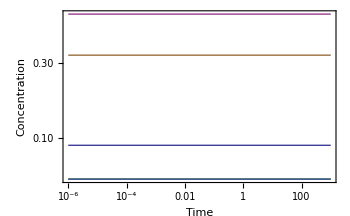

```mathematica
plotSimulation[simulate[model,{t,0,1000}][[1]],FrameLabel->{"Time","Concentration"}]
```

```mathematica
This graph the initial steady state concentrations of the x's with concentration vs. time.
```

```mathematica
{ssConc,ssFluxes}=findSteadyState[model,"Strategy"->simulate];
```

```mathematica
ssConc
```

{x1→0.0900993 Millimole Liter^-1,x2→0.0549503 Millimole Liter^-1,x3→0.0549503 Millimole Liter^-1,x4→0.0549503 Millimole Liter^-1,x5→0.0549503 Millimole Liter^-1,x6→0.609886 Millimole Liter^-1,x7→0.335134 Millimole Liter^-1}

```mathematica
{ssConcAfterPerturb,ssFluxesAfterPerturb}=findSteadyState[model,"Strategy"->simulate,Parameters->{Subscript[k, b1]^⟶ -> 10*(0.1/Hour)}]
```

{{x1→1.44575 Millimole Liter^-1,x2→0.277124 Millimole Liter^-1,x3→0.277124 Millimole Liter^-1,x4→0.277124 Millimole Liter^-1,x5→0.277124 Millimole Liter^-1,x6→0.191681 Millimole Liter^-1,x7→0.531195 Millimole Liter^-1},{v_b1→1. Millimole Hour^-1 Liter^-1,v_0→0.722876 Millimole Hour^-1,v_1→0.277124 Millimole Hour^-1,v_2→0.277124 Millimole Hour^-1,v_3→0.277124 Millimole Hour^-1,v_4→0.277124 Millimole Hour^-1,v_5→0.277124 Millimole Hour^-1,v_6→0. Millimole Hour^-1}}

```mathematica
ss1=stripUnits[ssFluxes[[All,2]]]
ss2=stripUnits[ssFluxesAfterPerturb[[All,2]]]
```

{0.1,0.0450497,0.0549503,0.0549503,0.0549503,0.0549503,0.0549503,0.}

{1.,0.722876,0.277124,0.277124,0.277124,0.277124,0.277124,0.}

```mathematica
null=NullSpace[model]ᵀ;
```

```mathematica
ss1Loadings=PseudoInverse[null].ss1
ss2Loadings=PseudoInverse[null].ss2
```

{0.0549503,0.0450497}

{0.277124,0.722876}

```mathematica
sumss1= Total[ss1Loadings]
sumss2=Total[ss2Loadings]
```

0.1

1.

```mathematica
ss1Loadings[[1]]/sumss1
ss2Loadings[[1]]/sumss2
```

0.549503

0.277124

```mathematica
Divide@@ss1Loadings
Divide@@ss2Loadings
```

1.21977

0.383363

```mathematica
Module[{concSol,fluxSol,ssConc,ssFluxes},
Manipulate[
{ssConc,ssFluxes}=findSteadyState[model,"Strategy"->simulate,Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1Liter/Hour)}];
GraphicsRow[{
BarChart[ssConc[[All,2]],PlotRange->{All,{-0.2,1.5}},ChartLabels->Placed[ssConc[[All,1]],Axis],PlotLabel->"Steady-state concentrations"],
BarChart[ssFluxes[[All,2]],PlotRange->{All,{-0.2,1.4}},ChartLabels->Placed[ssFluxes[[All,1]],Axis],PlotLabel->"Steady-state fluxes"]
},ImageSize->600]
,{{k0,1},0.5,10.}
]
]
```

```mathematica
The bar graphs here show how S-S fluxes and concentrations respond according to the changes produced by kO. Manipulations demonstrate how the various bars swift positions.
```

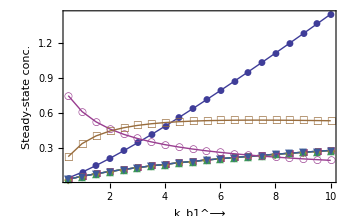

```mathematica
ListPlot[Transpose@Table[
{ssConc,ssFluxes}=findSteadyState[model,"Strategy"->simulate,Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1Liter/Hour)}];
Thread[{k0,stripUnits@ssConc[[All,2]]}]
,{k0,0.5,10.,.5}
],Joined->True,PlotMarkers->Automatic,Epilog->insetLegend[model["Species"]],FrameLabel->{Subscript[k, b1]^⟶,"Steady-state conc."}]
```

```mathematica
This graph shows the changes of x1-x7 in their steady-state concentrations through different parameters of kb1 forward.
```

### 1) Form the dimer first. You will borrow most of your code from Chapter 9 notebook.

```mathematica
additionalBindingReactions={Overscript[x5+x7⇌x8, 9],Overscript[x5+x8⇌x9, 10],Overscript[x5+x9⇌x10, 11]};
```

```mathematica
modelDimer=addReactions[model,{Overscript[x5+x7⇌x8, 9]}];
updateCustomRateLaws[modelDimer,{"6"->2 Subscript[k, 6]^⟶ x5[t] x6[t]-Subscript[k, 6]^⟵ x7[t],"9"->Subscript[k, 6]^⟶ x5[t] x7[t]-2 Subscript[k, 6]^⟵ x8[t]}]
```

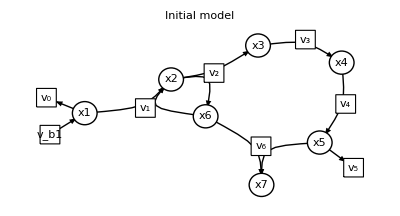

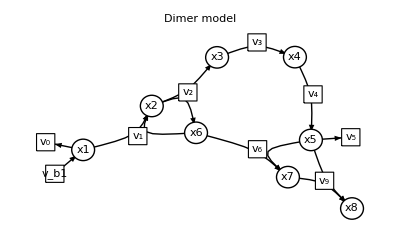

```mathematica
Show[showNetwork[model],PlotLabel->"Initial model"]
Show[showNetwork[modelDimer]/.{Subscript[v, 9]->Style[Subscript[v, 9],Background->Green,Larger],m["x8"]->Style[m["x8"],Background->Green,Larger]},PlotLabel->"Dimer model"]
```

### 2) Add the protein synthesis/degradation reactions.

```mathematica
synthAndDegradation=str2mass/@{"7: 0 <=> x6","8: x6 -> 0"};
modelWithProtSynth=addReactions[model,synthAndDegradation];
updateCustomRateLaws[modelWithProtSynth,{"7"->Subscript[k, 7]^⟶/(1+Underscript[K, 7] x5[t])}]
updateParameters[modelWithProtSynth,{Subscript[k, 7]^⟶->0.7 Hour^-1,Underscript[K, 7]->178,Subscript[k, 8]^⟶->0.1 Hour^-1}]
```

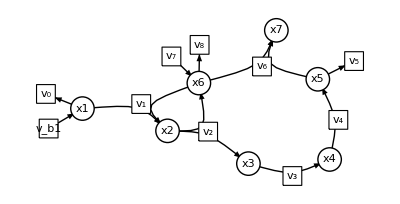

```mathematica
showNetwork[modelWithProtSynth]/.{pat:v["7"]:>Style[pat,Background->Red,Larger],pat:v["8"]->Style[pat,Background->Red,Larger]}
```

```mathematica
TableForm[Thread[{modelWithProtSynth["Reactions"],modelWithProtSynth["Rates"]}]]
```

(∅→x1)^b1 | x1^Xt k_b1^⟶
(x1→∅)^0 | k_0^⟶ x1[t]
(x1+x6→x2)^1 | k_1^⟶ x1[t] x6[t]
(x2→x3+x6)^2 | k_2^⟶ x2[t]
(x3→x4)^3 | k_3^⟶ x3[t]
(x4→x5)^4 | k_4^⟶ x4[t]
(x5→∅)^5 | k_5^⟶ x5[t]
(x5+x6⇌x7)^6 | k_6^⟶ x5[t] x6[t]-k_6^⟵ x7[t]
(∅⇌x6)^7 | k_7^⟶/(1+K_7 x5[t])
(x6→∅)^8 | k_8^⟶ x6[t]

### 3) Use the following initial conditions to update your model, they are from the dimer model without protein synthesis/degradation.

```mathematica
newIC = {x1->0.10619608924873525 Millimole Liter^-1,x2->0.04690195537563238 Millimole Liter^-1,x3->0.04690195537563238 Millimole Liter^-1,x4->0.04690195537563238 Millimole Liter^-1,x5->0.046901955375632354 Millimole Liter^-1,x6->0.44165426154043586 Millimole Liter^-1,x7->0.4142889693245482 Millimole Liter^-1,x8->0.0971548137593837 Millimole Liter^-1};
```

```mathematica
updateInitialConditions[modelDimer,newIC]
```

### 4) Simulate your model and plot it.

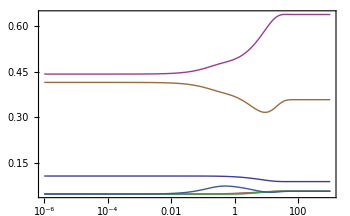

{x1→0.0878974 Millimole Liter^-1,x2→0.0560513 Millimole Liter^-1,x3→0.0560513 Millimole Liter^-1,x4→0.0560513 Millimole Liter^-1,x5→0.0560513 Millimole Liter^-1,x6→0.63769 Millimole Liter^-1,x7→0.357433 Millimole Liter^-1}

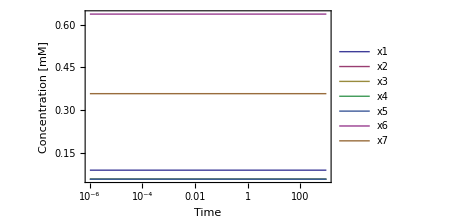

```mathematica
updateInitialConditions[modelWithProtSynth,newIC]
{concSolDimer,fluxSolDimer}=simulate[modelWithProtSynth,{t,0,1000}];
plotSimulation[concSolDimer,PlotFunction->LogLinearPlot]
steadystate=concSolDimer/.t->1000
updateInitialConditions[modelWithProtSynth,steadystate]
{concSolDimerSS,fluxSolDimerSS}=simulate[modelWithProtSynth,{t,0,1000}];
plotSimulation[concSolDimerSS,FrameLabel->{"Time","Concentration [mM]"},PlotFunction->LogLinearPlot,Legend->True]
```

```mathematica
The first graph demonstrates how the steady state is reached, while the second plot shows that the steady state is maintained since concentrations do not change over a range of time.
```

```mathematica
Module[{concSol,fluxSol},
Manipulate[
{concSol,fluxSol}=simulate[modelDimer,{t,0,tfinal},Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1/Hour)},InitialConditions->{m["x8"]->0Millimole Liter^-1}];
GraphicsGrid[{
{plotSimulation[concSol,FrameLabel->{"t","Concentration [mM]"},PlotFunction->Plot],
plotSimulation[fluxSol,FrameLabel->{"t","Fluxes [mM h^-1]"},PlotFunction->Plot]},
{plotSimulation[FilterRules[fluxSol,{v["1"],v["5"]}],FrameLabel->{"t","Fluxes [mM h^-1]"},PlotFunction->Plot,Legend->True,PlotStyle->{Black,Directive[Black,Dashed]}],Show[plotPhasePortrait[FilterRules[fluxSol,{v["1"],v["5"]}],ColorFunction->None,PlotRange->{{0,1.2},{0,1.2}},Mesh->{{.1,1,10,100}},MeshStyle->Directive[PointSize[.03],Red]],Graphics[{Dashed,Line[{{-1,-1},{2.5,2.5}}]}]]}
},ImageSize->600],{{k0,10,Subscript[k, b1]^⟶},0.5,100.},{{tfinal,40},.1,1000}
]
]
```

```mathematica
These plots show that all metabolite concentrations reach steady state (top left graph). The top right graph also shows that fluxes reach steady state at the same time scale as the concentrations. The bottom graphs describe v1 and v5 through a concentration vs. time plot and a phase portrait. At steady state v1=v5.
```

### 5) You should achieve a new steady state. Use this new steady state as your initial conditions for your final dimer model. When you make the change, plot the concentrations to make sure that they remain steady.

```mathematica
ss=concSolDimer/.t->1000 ;
updateInitialConditions[modelDimer,ss] 
{concSolDimerSS,fluxSolDimerSS}=simulate[modelDimer{t,0,1000}];plotSimulation[concSolDimerSS,FrameLabel->{"Time","Concentration"},PlotFunction->LogLinearPlot,Legend->True]
```

### Now, do the same 5 steps for the tetramer.

```mathematica
modelTetramer=addReactions[model,additionalBindingReactions];
updateCustomRateLaws[modelTetramer,{"6"->4 Subscript[k, 6]^⟶ x5[t] x6[t]-Subscript[k, 6]^⟵ x7[t],"9"->3 Subscript[k, 6]^⟶ x5[t] x7[t]-2 Subscript[k, 6]^⟵ x8[t],"10"->2 Subscript[k, 6]^⟶ x5[t] x7[t]-3 Subscript[k, 6]^⟵ x9[t],"11"->Subscript[k, 6]^⟶ x5[t] x7[t]-4 Subscript[k, 6]^⟵ x10[t]}]
```

```mathematica
Protein synthesis and degradation:
```

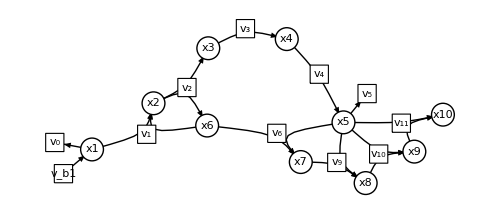

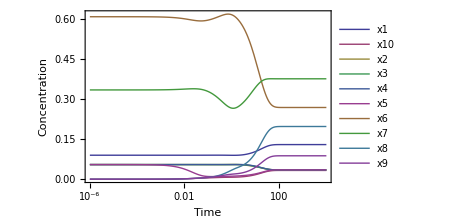

```mathematica
Show[showNetwork[modelTetramer]/.(v[getID[#]]->Style[v[getID[#]],Background->Green,Larger]&/@additionalBindingReactions),ImageSize->500]
{concSolTetramer,fluxSolTetramer}=simulate[modelTetramer,{t,0,10000},InitialConditions->{m["x8"]->0Millimole Liter^-1,m["x9"]->0Millimole Liter^-1,m["x10"]->0Millimole Liter^-1}];
plotSimulation[concSolTetramer,PlotFunction->LogLinearPlot,Legend->True,FrameLabel->{"Time","Concentration"}]
```

```mathematica
This graph shows that all the tetramer concentrations reach steady state over a range of time.
```

```mathematica
TableForm[ssEq=modelTetramer["ODE"]/.Derivative[1][_metabolite][t]:>0/.elem_[t]:>elem]
Dimensions[modelTetramer][[1]]-MatrixRank[modelTetramer]
NullSpace[modelTetramerᵀ]
conservationRelations=MapIndexed[C[First@#2]==#&,NullSpace[modelTetramerᵀ].modelTetramer["Species"]]
```

0==-x1 k_0^⟶-x1 x6 k_1^⟶+x1^Xt k_b1^⟶
0==x1 x6 k_1^⟶-x2 k_2^⟶
0==x2 k_2^⟶-x3 k_3^⟶
0==x3 k_3^⟶-x4 k_4^⟶
0==x4 k_4^⟶-x5 k_5^⟶+4 x10 k_6^⟵+x7 k_6^⟵+2 x8 k_6^⟵+3 x9 k_6^⟵-4 x5 x6 k_6^⟶-6 x5 x7 k_6^⟶
0==-x1 x6 k_1^⟶+x2 k_2^⟶+x7 k_6^⟵-4 x5 x6 k_6^⟶
0==-x7 k_6^⟵+2 x8 k_6^⟵+4 x5 x6 k_6^⟶-3 x5 x7 k_6^⟶
0==-2 x8 k_6^⟵+3 x9 k_6^⟵+x5 x7 k_6^⟶
0==4 x10 k_6^⟵-3 x9 k_6^⟵+x5 x7 k_6^⟶
0==-4 x10 k_6^⟵+x5 x7 k_6^⟶

1

{{0,1,0,0,0,1,1,1,1,1}}

{C[1]==x10+x2+x6+x7+x8+x9}

```mathematica
synthAndDegradation=str2mass/@{"7: 0 <=> x6","8: x6 -> 0"};
TetramermodelWithProtSynth=addReactions[model,synthAndDegradation];
updateCustomRateLaws[TetramermodelWithProtSynth,{"7"->Subscript[k, 7]^⟶/(1+Underscript[K, 7] x5[t])}]
updateParameters[TetramermodelWithProtSynth,{Subscript[k, 7]^⟶->0.7 Hour^-1,Underscript[K, 7]->178,Subscript[k, 8]^⟶->0.1 Hour^-1}]
showNetwork[TetramermodelWithProtSynth]/.{pat:v["7"]:>Style[pat,Background->Red,Larger],pat:v["8"]->Style[pat,Background->Red,Larger]}
```

-Graphics-

```mathematica
ssSol=Solve[Join[ssEq,conservationRelations],modelTetramer["Species"]];
newIC=(ssSol/.C[1]->1/.Dispatch[stripUnits[modelTetramer["Parameters"]]])[[1]];
updateInitialConditions[modelTetramer,#[[1]]->#[[2]]Millimole Liter^-1&/@newIC]
```

### Verify that the tetramer is a more effective mechanism than the dimer for rejecting disturbance when feedback of protein synthesis is included. You wil need the manipulate function at the end of chapter 9 notebook.

```mathematica
Module[{concSol,fluxSol,concSolDimer,fluxSolDimer,concSolTetramer,fluxSolTetramer},
Manipulate[
{concSol,fluxSol}=simulate[model,{t,0,tfinal},Parameters->{Subscript[k, b1]^⟶ -> k0(.1/Hour)}];
{concSolDimer,fluxSolDimer}=simulate[modelDimer,{t,0,tfinal},Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1/Hour)}];
{concSolTetramer,fluxSolTetramer}=simulate[modelTetramer,{t,0,tfinal},Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1/Hour)}];
Show[plotPhasePortrait[FilterRules[#,{v["1"],v["5"]}]&/@{fluxSol,fluxSolDimer,fluxSolTetramer},ColorFunction->None,PlotRange->{{0,1.2},{0,1.2}},Mesh->{{.1,1,10,100}},MeshStyle->Directive[PointSize[.03],Red],PlotStyle->Thick],Graphics[{Dashed,Line[{{-1,-1},{2.5,2.5}}]}],FrameLabel->{v["1"],v["5"]}],{{k0,10,Subscript[k, b1]^⟶},0.5,100.},{{tfinal,40},.1,1000}
]
]
```

```mathematica
The tetramer which is represented by the green line reaches steady state faster than the blue and purple models which represent initial feedback and the dimer respectively. The tetramer is therefore a more responspive model and returns to steady state from disturbance much quicker.
```

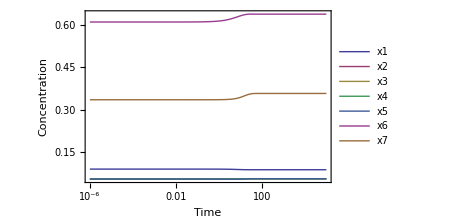

```mathematica
{concSolTetramer,fluxSolTetramer}=simulate[TetramermodelWithProtSynth,{t,0,1*^5}];plotSimulation[concSolTetramer,FrameLabel->{"Time","Concentration"},PlotFunction->LogLinearPlot,Legend->True]
```

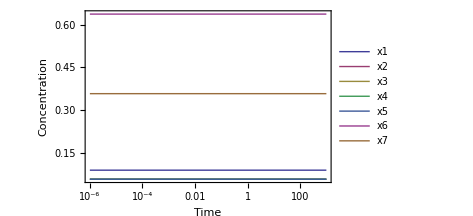

```mathematica
ssT=concSolTetramer/.t->1000 ;
updateInitialConditions[TetramermodelWithProtSynth,ssT] 
{concSolTetramerSS,fluxSolTetramerSS}=simulate[TetramermodelWithProtSynth,{t,0,1000}];plotSimulation[concSolTetramerSS,FrameLabel->{"Time","Concentration"},PlotFunction->LogLinearPlot,Legend->True]
```

```mathematica
This final plot shows that using steady state concentrations as new initial conditions results in constant continued steady state for all variables.
```

### Now do parts ii) and iii). For part ii) you need to make two pools, plot them vs. time, and compare them. For part iii) play around with the original model parameters to see what will greatly improve the disturbance rejection for all three enzyme forms.

```mathematica
ii.
```

```mathematica
modelD=modelDimer;
modelT=modelTetramer;
```

```mathematica
f2=(m["x7",None]+2*m["x8",None])/(2*(m["x7",None]+m["x8",None]));
f4=(m["x7",None]+2*m["x8",None]+3*m["x9",None]+4*m["x10",None])/(4*(m["x7",None]+m["x8",None]+m["x9",None]+m["x10",None]));
poolD={"f2"-> (m["x7",None]+2*m["x8",None])/(2*(m["x7",None]+m["x8",None]))};
poolT={"f4"-> (m["x7",None]+2*m["x8",None]+3*m["x9",None]+4*m["x10",None])/(4*(m["x7",None]+m["x8",None]+m["x9",None]+m["x10",None]))};
```

```mathematica
concSolD=simulate[modelD,{t,0,1*^4}][[1]];
plotSimulation[poolD/.modelD["Parameters"]/.concSolD,{t,0,1*^8},PlotFunction->Plot,FrameLabel->{"Time","Fraction of inhibited enzyme"},PlotLabel->"Fraction Inhibited vs. Time for Dimer"]
```

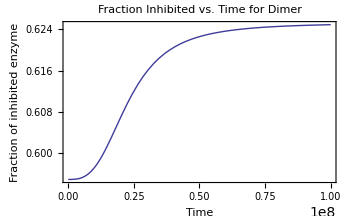

```mathematica
The graph shows the behavior of dimer enzymes against time in response to the inhibitor, the fraction levels off asymptotically at 0.625 after increasing.
```

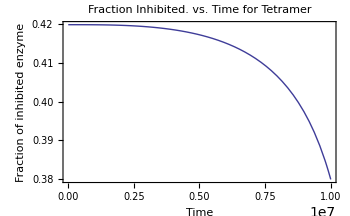

```mathematica
concSolT=simulate[modelT,{t,0,1*^4}][[1]];
plotSimulation[poolT/.modelT["Parameters"]/.concSolT,{t,0,1*^7},PlotFunction->Plot,FrameLabel->{"Time","Fraction of inhibited enzyme"},PlotLabel->"Fraction Inhibited. vs. Time for Tetramer"]
```

```mathematica
As opposed to the dimer model the tetramer model decreases inhibited fraction as time moves forward showing that the tetramer model is much better at responding to inhibition and returning to normal function.
```

```mathematica
iii.
```

```mathematica
The above data has shown that to greatly improve the disturbance regection for all 3 enzymes increase kb1 since a high value of kb1 results in instant rejection which cannot be seen at low values of kb1. Increasing tfinal has little effect on the rejection of any of the enzyme forms.
```